# Лабораторная работа 2.

Выполнила студентка ММФ БГУ
КМ, 1к., 5 гр. Ковалевская В.С. 
15 сентября 2021

## 1. Построение дерева выражения

### Задание 1.1

```mathematica
-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)
```

-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz

```mathematica
1/(√(2+x^2)(-1+x^4))
```

1/(√(2+x^2) (-1+x^4))

π, ∞, ⅇ, ⅈ

Superscript: Ctrl+6, Ctrl+ -, Ctrl+5
Fraction: Ctrl+/,
Radical: Ctrl+2, Ctrl+5

### Задание 1.2

```mathematica
-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)//StandardForm
```

-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz

```mathematica
-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)//FullForm
```

Plus[Rational[-1,5],E,Times[Complex[1,-2],Power[Plus[Times[-0.4,x],Times[3,y]],-1]],Power[z,Times[6,x]],Times[-7,\[Pi]xz]]

```mathematica
expr1=-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)
?expr1
```

-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz

```mathematica
myExpr=1/(√(2+x^2)(-1+x^4))
?myExpr
```

1/(√(2+x^2) (-1+x^4))

```mathematica
myExpr=1/(√(2+x^2)(-1+x^4))
myExpr//StandardForm
```

1/(√(2+x^2) (-1+x^4))

1/(√(2+x^2) (-1+x^4))

```mathematica
myExpr//FullForm
```

Times[Power[Plus[2,Power[x,2]],Rational[-1,2]],Power[Plus[-1,Power[x,4]],-1]]

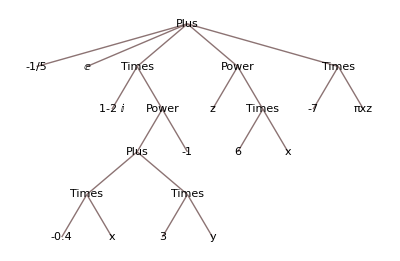

```mathematica
TreeForm[expr1]
```

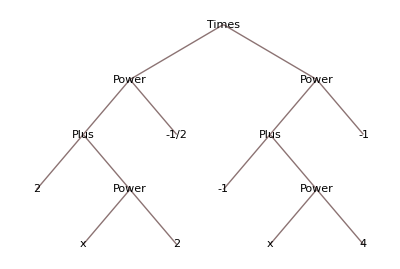

```mathematica
TreeForm[1/(√(2+x^2)(-1+x^4))]
```

## 2. Анализ структуры выражения

### Задание 2.1

Изучите возможности исследования структуры выражения посредством функций Level, Depth . Используйте в качестве примеров выражение (1.1) и выражение Вашего варианта .

```mathematica
expr1=-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)
?expr1
```

-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz

```mathematica
TreeForm[expr1]
```

-Graphics-

```mathematica
myExpr=1/(√(2+x^2)(-1+x^4))
?myExpr
```

1/(√(2+x^2) (-1+x^4))

```mathematica
TreeForm[1/(√(2+x^2)(-1+x^4))]
```

-Graphics-

```mathematica
Level[expr1, Infinity]
```

{-1/5,ⅇ,1-2 ⅈ,-0.4,x,-0.4 x,3,y,3 y,-0.4 x+3 y,-1,1/(-0.4 x+3 y),(1-2 ⅈ)/(-0.4 x+3 y),z,6,x,6 x,z^(6 x),-7,πxz,-7 πxz}

Нулевой уровень соответствует всему выражению expr1, любого выражения.

```mathematica
Depth[expr1]
```

6

n_max=Depth[expr]-1

```mathematica
Level[expr1, {4,5}]
```

{-0.4,x,-0.4 x,3,y,3 y}

```mathematica
Level[expr1, {Depth[expr1]-1}]
```

{-0.4,x,3,y}

n_max=5

```mathematica
Level[expr1, {1}]
```

{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),z^(6 x),-7 πxz}

```mathematica
Level[expr1, {2}]
```

{1-2 ⅈ,1/(-0.4 x+3 y),z,6 x,-7,πxz}

```mathematica
Level[expr1, {Depth[expr1]-1}]
```

{-0.4,x,3,y}

```mathematica
Level[expr1, {Depth[expr1]-2}]
```

{-0.4 x,3 y}

```mathematica
Level[expr1, {1}]
```

{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),z^(6 x),-7 πxz}

### Задание 2.2

Форматируйте структуру выражения (1.1), используя функции Head, 
Table, MatrixForm. Используйте чистые (анонимные, безымянные) 
функции и функцию Map.

```mathematica
Table[Level[expr1,{i}],{i, Depth[expr1]-1}]
```

{{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),z^(6 x),-7 πxz},{1-2 ⅈ,1/(-0.4 x+3 y),z,6 x,-7,πxz},{-0.4 x+3 y,-1,6,x},{-0.4 x,3 y},{-0.4,x,3,y}}

```mathematica
Table[Level[expr1,{i}],{i, Depth[expr1]-1}]//MatrixForm
```

({-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),z^(6 x),-7 πxz}
{1-2 ⅈ,1/(-0.4 x+3 y),z,6 x,-7,πxz}
{-0.4 x+3 y,-1,6,x}
{-0.4 x,3 y}
{-0.4,x,3,y})

```mathematica
Head/@Level[expr1, {1}]
```

{Rational,Symbol,Times,Power,Times}

Голова первого уровня.

```mathematica
Head/@Level[expr1, {2}]
```

{Complex,Power,Symbol,Times,Integer,Symbol}

Голова 2-го уровня.

```mathematica
Head/@Level[expr1, {0, Depth[expr1]-1}]
```

{Rational,Symbol,Complex,Real,Symbol,Times,Integer,Symbol,Times,Plus,Integer,Power,Times,Symbol,Integer,Symbol,Times,Power,Integer,Symbol,Times,Plus}

Голова i-ого уровня.

```mathematica
Table[Head/@Level[expr1,  {0, Depth[expr1]-1}], {i,0,Depth[expr1]-1}]//MatrixForm
```

(Rational | Symbol | Complex | Real | Symbol | Times | Integer | Symbol | Times | Plus | Integer | Power | Times | Symbol | Integer | Symbol | Times | Power | Integer | Symbol | Times | Plus
Rational | Symbol | Complex | Real | Symbol | Times | Integer | Symbol | Times | Plus | Integer | Power | Times | Symbol | Integer | Symbol | Times | Power | Integer | Symbol | Times | Plus
Rational | Symbol | Complex | Real | Symbol | Times | Integer | Symbol | Times | Plus | Integer | Power | Times | Symbol | Integer | Symbol | Times | Power | Integer | Symbol | Times | Plus
Rational | Symbol | Complex | Real | Symbol | Times | Integer | Symbol | Times | Plus | Integer | Power | Times | Symbol | Integer | Symbol | Times | Power | Integer | Symbol | Times | Plus
Rational | Symbol | Complex | Real | Symbol | Times | Integer | Symbol | Times | Plus | Integer | Power | Times | Symbol | Integer | Symbol | Times | Power | Integer | Symbol | Times | Plus
Rational | Symbol | Complex | Real | Symbol | Times | Integer | Symbol | Times | Plus | Integer | Power | Times | Symbol | Integer | Symbol | Times | Power | Integer | Symbol | Times | Plus)

```mathematica
{Head[#],#}&/@Level[expr1,  {0, Depth[expr1]-1}]
```

{{Rational,-1/5},{Symbol,ⅇ},{Complex,1-2 ⅈ},{Real,-0.4},{Symbol,x},{Times,-0.4 x},{Integer,3},{Symbol,y},{Times,3 y},{Plus,-0.4 x+3 y},{Integer,-1},{Power,1/(-0.4 x+3 y)},{Times,(1-2 ⅈ)/(-0.4 x+3 y)},{Symbol,z},{Integer,6},{Symbol,x},{Times,6 x},{Power,z^(6 x)},{Integer,-7},{Symbol,πxz},{Times,-7 πxz},{Plus,-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz}}

```mathematica
{Head[#],#}&/@Level[expr1,  {0, Depth[expr1]-1}]//MatrixForm
```

(Rational | -1/5
Symbol | ⅇ
Complex | 1-2 ⅈ
Real | -0.4
Symbol | x
Times | -0.4 x
Integer | 3
Symbol | y
Times | 3 y
Plus | -0.4 x+3 y
Integer | -1
Power | 1/(-0.4 x+3 y)
Times | (1-2 ⅈ)/(-0.4 x+3 y)
Symbol | z
Integer | 6
Symbol | x
Times | 6 x
Power | z^(6 x)
Integer | -7
Symbol | πxz
Times | -7 πxz
Plus | -1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)

```mathematica
{Head[#],#}&/@Level[expr1, {0}]//MatrixForm
```

(Plus | -1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)

```mathematica
{Head[#],#}&/@Level[expr1, {1}]//MatrixForm
```

(Rational | -1/5
Symbol | ⅇ
Times | (1-2 ⅈ)/(-0.4 x+3 y)
Power | z^(6 x)
Times | -7 πxz)

```mathematica
{Head[#],#}&/@Level[expr1, {2}]//MatrixForm
```

(Complex | 1-2 ⅈ
Power | 1/(-0.4 x+3 y)
Symbol | z
Times | 6 x
Integer | -7
Symbol | πxz)

```mathematica
{Head[#],#}&/@Level[expr1, {3}]//MatrixForm
```

(Plus | -0.4 x+3 y
Integer | -1
Integer | 6
Symbol | x)

```mathematica
{Head[#],#}&/@Level[expr1, {4}]//MatrixForm
```

(Times | -0.4 x
Times | 3 y)

```mathematica
{Head[#],#}&/@Level[expr1, {5}]//MatrixForm
```

(Real | -0.4
Symbol | x
Integer | 3
Symbol | y)

```mathematica
Table[{Head[#],#}&/@Level[expr1,  {0, Depth[expr1]-1}],{i, 0, Depth[expr1]-1}]//MatrixForm
```

((Rational
-1/5) | (Symbol
ⅇ) | (Complex
1-2 ⅈ) | (Real
-0.4) | (Symbol
x) | (Times
-0.4 x) | (Integer
3) | (Symbol
y) | (Times
3 y) | (Plus
-0.4 x+3 y) | (Integer
-1) | (Power
1/(-0.4 x+3 y)) | (Times
(1-2 ⅈ)/(-0.4 x+3 y)) | (Symbol
z) | (Integer
6) | (Symbol
x) | (Times
6 x) | (Power
z^(6 x)) | (Integer
-7) | (Symbol
πxz) | (Times
-7 πxz) | (Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)
(Rational
-1/5) | (Symbol
ⅇ) | (Complex
1-2 ⅈ) | (Real
-0.4) | (Symbol
x) | (Times
-0.4 x) | (Integer
3) | (Symbol
y) | (Times
3 y) | (Plus
-0.4 x+3 y) | (Integer
-1) | (Power
1/(-0.4 x+3 y)) | (Times
(1-2 ⅈ)/(-0.4 x+3 y)) | (Symbol
z) | (Integer
6) | (Symbol
x) | (Times
6 x) | (Power
z^(6 x)) | (Integer
-7) | (Symbol
πxz) | (Times
-7 πxz) | (Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)
(Rational
-1/5) | (Symbol
ⅇ) | (Complex
1-2 ⅈ) | (Real
-0.4) | (Symbol
x) | (Times
-0.4 x) | (Integer
3) | (Symbol
y) | (Times
3 y) | (Plus
-0.4 x+3 y) | (Integer
-1) | (Power
1/(-0.4 x+3 y)) | (Times
(1-2 ⅈ)/(-0.4 x+3 y)) | (Symbol
z) | (Integer
6) | (Symbol
x) | (Times
6 x) | (Power
z^(6 x)) | (Integer
-7) | (Symbol
πxz) | (Times
-7 πxz) | (Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)
(Rational
-1/5) | (Symbol
ⅇ) | (Complex
1-2 ⅈ) | (Real
-0.4) | (Symbol
x) | (Times
-0.4 x) | (Integer
3) | (Symbol
y) | (Times
3 y) | (Plus
-0.4 x+3 y) | (Integer
-1) | (Power
1/(-0.4 x+3 y)) | (Times
(1-2 ⅈ)/(-0.4 x+3 y)) | (Symbol
z) | (Integer
6) | (Symbol
x) | (Times
6 x) | (Power
z^(6 x)) | (Integer
-7) | (Symbol
πxz) | (Times
-7 πxz) | (Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)
(Rational
-1/5) | (Symbol
ⅇ) | (Complex
1-2 ⅈ) | (Real
-0.4) | (Symbol
x) | (Times
-0.4 x) | (Integer
3) | (Symbol
y) | (Times
3 y) | (Plus
-0.4 x+3 y) | (Integer
-1) | (Power
1/(-0.4 x+3 y)) | (Times
(1-2 ⅈ)/(-0.4 x+3 y)) | (Symbol
z) | (Integer
6) | (Symbol
x) | (Times
6 x) | (Power
z^(6 x)) | (Integer
-7) | (Symbol
πxz) | (Times
-7 πxz) | (Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)
(Rational
-1/5) | (Symbol
ⅇ) | (Complex
1-2 ⅈ) | (Real
-0.4) | (Symbol
x) | (Times
-0.4 x) | (Integer
3) | (Symbol
y) | (Times
3 y) | (Plus
-0.4 x+3 y) | (Integer
-1) | (Power
1/(-0.4 x+3 y)) | (Times
(1-2 ⅈ)/(-0.4 x+3 y)) | (Symbol
z) | (Integer
6) | (Symbol
x) | (Times
6 x) | (Power
z^(6 x)) | (Integer
-7) | (Symbol
πxz) | (Times
-7 πxz) | (Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz))

### Задание 2.3

Изучите возможности исследования структуры выражения посредством функций AtomQ, Position, Part, Take, Length. Используйте выражение (1.1) в качестве примера.

```mathematica
Position[expr1,x]
```

{{3,2,1,1,2},{4,2,2}}

```mathematica
Position[expr1,y]
```

{{3,2,1,2,2}}

```mathematica
Position[expr1,z]
```

{{4,1}}

```mathematica
expr1[[-1]]
```

-7 πxz

```mathematica
expr1[[-2]]
```

z^(6 x)

```mathematica
expr1[[-1,1]]
```

-7

```mathematica
Take[expr1, -2]
```

z^(6 x)-7 πxz

```mathematica
Take[Level[expr1, {2}], {-2}]
```

{-7}

```mathematica
AtomQ/@Table[Level[expr1, {1}]]
```

{True,True,False,False,False}

Функции Part, Take используются для извлечения части выражения.
Функция AtomQ определяет, является ли выражение атомарным. Take - спецификатор последовательности, Part - спецификатор уровней.

## 3. Разложение выражения по уровням

### Задание 3.1

Создайте функцию myExprLevels[expr], возвращающую произвольное выражение expr в виде подвыражений, разложенных по уровням. Для каждого уровня выражения expr функция myExprLevels отображает подвыражения, которые находятся на указанном уровне, а также головы этих подвыражений.

```mathematica
myExprLevels[expr_]:=Table[MatrixForm[{Head[#],#}]]&/@Level[expr,{i}],{i, 0, Depth[expr1]-1}
```

```mathematica
Do[Print[i,":", myExprLevels[expr1]],{i,0,Depth[expr1]-1}]
```

0:{(Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)}

1:{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Power
z^(6 x)),(Times
-7 πxz)}

2:{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Symbol
z),(Times
6 x),(Integer
-7),(Symbol
πxz)}

3:{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)}

4:{(Times
-0.4 x),(Times
3 y)}

5:{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)}

### Задание 3.2

Разложите выражение (1.1) по уровням, используя функцию 
myExprLevels, построенную ранее. Определите позицию каждого 
атомарного объекта выражения (1.1). Результаты оформите в виде таблицы.

```mathematica
Print[{Table[Level[expr1,{-1}],{1}]}, {Position[expr1, z], Position[expr1, -1/5],Position[expr1, ⅇ],Position[expr1, 1-2ⅈ],Position[expr1, -0.4],Position[expr1, x],Position[expr1, y],Position[expr1, -1],Position[expr1, -7],Position[expr1, π],Position[expr1, 6],Position[expr1, 3]}]
```

{{{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,-1,z,6,x,-7,πxz}}}{{{4,1}},{{1}},{{2}},{{3,1}},{{3,2,1,1,1}},{{3,2,1,1,2},{4,2,2}},{{3,2,1,2,2}},{{3,2,2}},{{5,1}},{},{{4,2,1}},{{3,2,1,2,1}}}

```mathematica
Grid[{{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,-1,z,6,x,-7,πxz}, {{{4,1}},{{1}},{{2}},{{3,1}},{{3,2,1,1,1}},{{3,2,1,1,2},{4,2,2}},{{3,2,1,2,2}},{{3,2,2}},{{5,1}},{},{{4,2,1}},{{3,2,1,2,1}}}}, Frame->All]
```

-1/5 | ⅇ | 1-2 ⅈ | -0.4 | x | 3 | y | -1 | z | 6 | x | -7 | πxz
{{4,1}} | {{1}} | {{2}} | {{3,1}} | {{3,2,1,1,1}} | {{3,2,1,1,2},{4,2,2}} | {{3,2,1,2,2}} | {{3,2,2}} | {{5,1}} | {} | {{4,2,1}} | {{3,2,1,2,1}} |

## 4. Анализ моего выражения, вариант 5

### 2.1

```mathematica
myExpr=1/(√(2+x^2)(-1+x^4))
?myExpr
```

1/(√(2+x^2) (-1+x^4))

```mathematica
TreeForm[myExpr]
```

-Graphics-

```mathematica
Level[myExpr, Infinity]
```

{2,x,2,x^2,2+x^2,-1/2,1/(√(2+x^2)),-1,x,4,x^4,-1+x^4,-1,1/(-1+x^4)}

```mathematica
Depth[myExpr]
```

5

```mathematica
Level[expr1, {3,4}]
```

{-0.4 x,3 y,-0.4 x+3 y,-1,6,x}

```mathematica
Level[myExpr, {Depth[myExpr]-1}]
```

{x,2,x,4}

```mathematica
Level[myExpr, {-1}]
```

{2,x,2,-1/2,-1,x,4,-1}

```mathematica
Level[myExpr, {-2}]
```

{x^2,x^4}

```mathematica
Level[myExpr, {Depth[myExpr]-1}]
```

{x,2,x,4}

```mathematica
Level[myExpr, {Depth[myExpr]-2}]
```

{2,x^2,-1,x^4}

### 2.2

```mathematica
Table[Level[myExpr,{i}],{i, Depth[myExpr]-1}]
```

{{1/(√(2+x^2)),1/(-1+x^4)},{2+x^2,-1/2,-1+x^4,-1},{2,x^2,-1,x^4},{x,2,x,4}}

```mathematica
Table[Level[myExpr,{i}],{i, Depth[myExpr]-1}]//MatrixForm
```

({1/(√(2+x^2)),1/(-1+x^4)}
{2+x^2,-1/2,-1+x^4,-1}
{2,x^2,-1,x^4}
{x,2,x,4})

```mathematica
Head/@Level[myExpr, {1}]
```

{Power,Power}

```mathematica
Head/@Level[myExpr, {2}]
```

{Plus,Rational,Plus,Integer}

```mathematica
Head/@Level[myExpr,  {0, Depth[myExpr]-1}]
```

{Integer,Symbol,Integer,Power,Plus,Rational,Power,Integer,Symbol,Integer,Power,Plus,Integer,Power,Times}

```mathematica
Table[Head/@Level[myExpr,   {0, Depth[myExpr]-1}], {i,0,Depth[myExpr-1]}]//MatrixForm
```

(Integer | Symbol | Integer | Power | Plus | Rational | Power | Integer | Symbol | Integer | Power | Plus | Integer | Power | Times
Integer | Symbol | Integer | Power | Plus | Rational | Power | Integer | Symbol | Integer | Power | Plus | Integer | Power | Times
Integer | Symbol | Integer | Power | Plus | Rational | Power | Integer | Symbol | Integer | Power | Plus | Integer | Power | Times
Integer | Symbol | Integer | Power | Plus | Rational | Power | Integer | Symbol | Integer | Power | Plus | Integer | Power | Times
Integer | Symbol | Integer | Power | Plus | Rational | Power | Integer | Symbol | Integer | Power | Plus | Integer | Power | Times
Integer | Symbol | Integer | Power | Plus | Rational | Power | Integer | Symbol | Integer | Power | Plus | Integer | Power | Times
Integer | Symbol | Integer | Power | Plus | Rational | Power | Integer | Symbol | Integer | Power | Plus | Integer | Power | Times)

```mathematica
{Head[#],#}&/@Level[myExpr, {0}]//MatrixForm
```

(Times | 1/(√(2+x^2) (-1+x^4)))

```mathematica
{Head[#],#}&/@Level[myExpr, {1}]//MatrixForm
```

(Power | 1/(√(2+x^2))
Power | 1/(-1+x^4))

```mathematica
{Head[#],#}&/@Level[myExpr, {2}]//MatrixForm
```

(Plus | 2+x^2
Rational | -1/2
Plus | -1+x^4
Integer | -1)

```mathematica
{Head[#],#}&/@Level[myExpr, {3}]//MatrixForm
```

(Integer | 2
Power | x^2
Integer | -1
Power | x^4)

```mathematica
{Head[#],#}&/@Level[myExpr, {4}]//MatrixForm
```

(Symbol | x
Integer | 2
Symbol | x
Integer | 4)

### 2.3

Изучите возможности исследования структуры выражения посредством функций AtomQ, Position, Part, Take, Length. Используйте выражение (1.1) в качестве примера.

```mathematica
Position[myExpr,x]
```

{{1,1,2,1},{2,1,2,1}}

```mathematica
Position[myExpr,y]
```

{}

```mathematica
Position[myExpr,z]
```

{}

```mathematica
myExpr[[-1]]
```

1/(-1+x^4)

```mathematica
myExpr[[-2]]
```

1/(√(2+x^2))

```mathematica
myExpr[[-1,1]]
```

-1+x^4

```mathematica
Take[myExpr, -2]
```

1/(√(2+x^2) (-1+x^4))

```mathematica
Take[Level[myExpr, {2}], {-2}]
```

{-1+x^4}

```mathematica
AtomQ/@Table[Level[myExpr, {1}]]
```

{False,False}

Функции Part, Take используются для извлечения части выражения.
Функция AtomQ определяет, является ли выражение атомарным. Take - спецификатор последовательности, Part - спецификатор уровней.

### 3.1

Создайте функцию myExprLevels[expr], возвращающую произвольное выражение expr в виде подвыражений, разложенных по уровням. Для каждого уровня выражения expr функция myExprLevels отображает подвыражения, которые находятся на указанном уровне, а также головы этих подвыражений.

```mathematica
myExprLevels[expr_]:=MatrixForm[{Head[#],#}]&/@Level[expr,{i}]
```

```mathematica
Do[Print[i,":", myExprLevels[myExpr]],{i,0,Depth[myExpr]-1}]
```

0:{(Times
1/(√(2+x^2) (-1+x^4)))}

1:{(Power
1/(√(2+x^2))),(Power
1/(-1+x^4))}

2:{(Plus
2+x^2),(Rational
-1/2),(Plus
-1+x^4),(Integer
-1)}

3:{(Integer
2),(Power
x^2),(Integer
-1),(Power
x^4)}

4:{(Symbol
x),(Integer
2),(Symbol
x),(Integer
4)}

### 3.2

Разложите выражение (1.1) по уровням, используя функцию 
myExprLevels, построенную ранее. Определите позицию каждого 
атомарного объекта выражения (1.1). Результаты оформите в виде таблицы.

```mathematica
Grid[{Level[expr1, {-1}]}{Position}]
```

-(Position/5) | ⅇ Position | (1-2 ⅈ) Position | -0.4 Position | Position x | 3 Position | Position y | -Position | Position z | 6 Position | Position x | -7 Position | Position πxz

```mathematica
Print[{Table[Level[myExpr,{-1}],{1}]}, {Position[myExpr, z], Position[myExpr, -1/5],Position[myExpr, ⅇ],Position[myExpr, 1-2ⅈ],Position[myExpr, -0.4],Position[myExpr, x],Position[myExpr, y],Position[myExpr, -1],Position[myExpr, -7],Position[myExpr, π],Position[myExpr, 6],Position[myExpr, 3]}]
```

{{{2,x,2,-1/2,-1,x,4,-1}}}{{},{},{},{},{},{{1,1,2,1},{2,1,2,1}},{},{{2,1,1},{2,2}},{},{},{},{}}

```mathematica
Grid[{{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,-1,z,6,x,-7,πxz}, {{{4,1}},{{1}},{{2}},{{3,1}},{{3,2,1,1,1}},{{3,2,1,1,2},{4,2,2}},{{3,2,1,2,2}},{{3,2,2}},{{5,1}},{},{{4,2,1}},{{3,2,1,2,1}}}}, Frame->All]
```

-1/5 | ⅇ | 1-2 ⅈ | -0.4 | x | 3 | y | -1 | z | 6 | x | -7 | πxz
{{4,1}} | {{1}} | {{2}} | {{3,1}} | {{3,2,1,1,1}} | {{3,2,1,1,2},{4,2,2}} | {{3,2,1,2,2}} | {{3,2,2}} | {{5,1}} | {} | {{4,2,1}} | {{3,2,1,2,1}} |